# Chapter 12 Examples+

## Ex 12.1

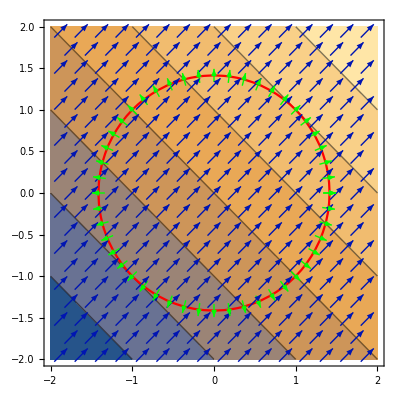

```mathematica
f[{x1_,x2_}]:= x1+x2
df[{x1_,x2_}]:={1,1}
c1[{x1_,x2_}]:= x1^2+x2^2-2
dc1[{x1_,x2_}]:={2x1,2x2}
points=Table[√2{Cos[θ],Sin[θ]},{θ,0, 2π,π/24}];
Show[
ContourPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2}],
ContourPlot[c1[{x1,x2}]==0,{x1,-2,2},{x2,-2,2},ContourStyle->Red],
VectorPlot[df[{x1,x2}],{x1,-2,2},{x2,-2,2}],
VectorPlot[dc1[{x1,x2}],{x1,-2,2},{x2,-2,2},VectorPoints->points,VectorColorFunction->None,VectorStyle->Green]
]
```

Lets identify in words where the max and min are.

## Ex 12.2

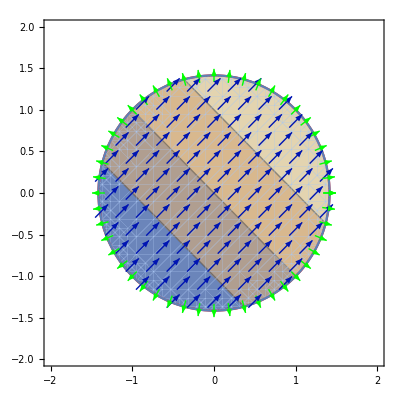

```mathematica
f[{x1_,x2_}]:= x1+x2
df[{x1_,x2_}]:={1,1}
c1[{x1_,x2_}]:= 2-(x1^2+x2^2)
dc1[{x1_,x2_}]:={2x1,2x2}
points=Table[√2{Cos[θ],Sin[θ]},{θ,0, 2π,π/24}];
Show[
ContourPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},
RegionFunction->Function[{x1,x2},c1[{x1,x2}]>0]],
ContourPlot[c1[{x1,x2}]==0,{x1,-2,2},{x2,-2,2},ContourStyle->Red],
VectorPlot[df[{x1,x2}],{x1,-2,2},{x2,-2,2},RegionFunction->Function[{x1,x2},c1[{x1,x2}]>0]],
VectorPlot[dc1[{x1,x2}],{x1,-2,2},{x2,-2,2},VectorPoints->points,VectorColorFunction->None,VectorStyle->Green]
]
```

## Ex 12.3

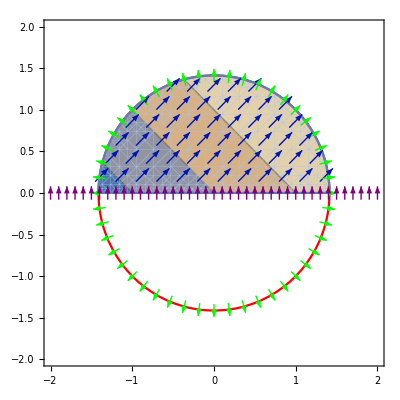

```mathematica
f[{x1_,x2_}]:= x1+x2
df[{x1_,x2_}]:={1,1}
c1[{x1_,x2_}]:= 2-(x1^2+x2^2)
c2[{x1_,x2_}]:= x2
dc1[{x1_,x2_}]:={2x1,2x2}
dc2[{x1_,x2_}]:={0,1}
c1points=Table[√2{Cos[θ],Sin[θ]},{θ,0, 2π,π/24}];
c2points=Table[{x1,0},{x1,-2.0,2,0.1}];
Show[
ContourPlot[f[{x1,x2}],{x1,-2,2},{x2,-2,2},
RegionFunction->Function[{x1,x2},And[c1[{x1,x2}]>0,c2[{x1,x2}]>0]]],
ContourPlot[c1[{x1,x2}]==0,{x1,-2,2},{x2,-2,2},ContourStyle->Red],
VectorPlot[df[{x1,x2}],{x1,-2,2},{x2,-2,2},RegionFunction->Function[{x1,x2},And[c1[{x1,x2}]>0,c2[{x1,x2}]>0]]],
VectorPlot[dc1[{x1,x2}],{x1,-2,2},{x2,-2,2},VectorPoints->c1points,VectorColorFunction->None,VectorStyle->Green],
VectorPlot[dc2[{x1,x2}],{x1,-2,2},{x2,-2,2},VectorPoints->c2points,VectorColorFunction->None,VectorStyle->Purple]
]
```